```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/lgz/Documents/llvm-curvefit/MemoryAnalysisCode

```mathematica
filter=ToExpression[StringCases[#1,#2~~x:DigitCharacter..->x]]&;
```

```mathematica
pdata=Import["papinfo","Text"];
```

```mathematica
rdata=Import["info","Text"];
```

```mathematica
pl1=filter[pdata,"PAPI_L1_TCH:"];
```

```mathematica
pl2=filter[pdata,"PAPI_L2_TCH:"];
```

```mathematica
rl1=filter[rdata,"HITL1:"];
```

```mathematica
rl2=filter[rdata,"HITL2:"];
```

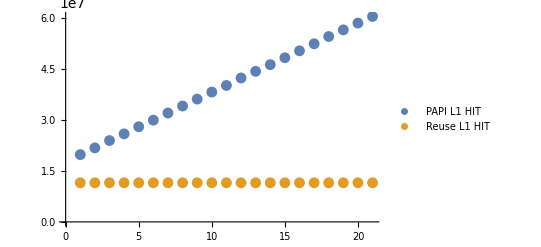

```mathematica
ListPlot[{pl1,rl1},PlotLegends->{"PAPI L1 HIT","Reuse L1 HIT"}]
```

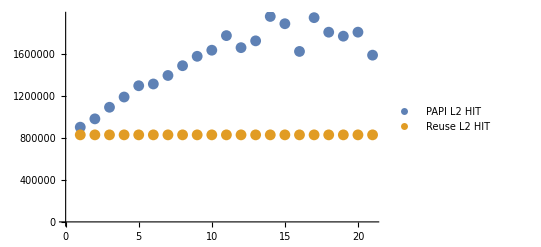

```mathematica
ListPlot[{pl2,rl2},PlotLegends->{"PAPI L2 HIT","Reuse L2 HIT"}]
```

```mathematica
rl1
```

{11502472,11502472,11502472,11502472,11502472,11502472,11502472,11502472,11502472,11502472,11502472,11502472,11502472,11502472,11502472,11502472,11502472,11502472,11502472,11502472,11502472}

```mathematica
rl2
```

{829759,829759,829759,829759,829759,829759,829759,829759,829759,829759,829759,829759,829759,829759,829759,829759,829759,829759,829759,829759,829759}

```mathematica
pl1
```

{19785934,21769192,23927786,25891810,27996555,29926576,32020676,34083603,36112893,38178667,40132549,42324248,44274997,46251802,48284571,50317609,52387033,54526071,56476533,58466926,60420588}